# SFS for single mutations

```mathematica
f[S_, x_] := (1 - E^(-S (1 - x)))/(x (1 - x) (1 - E^(-S)))

Q[n_, i_, x_] := n !/(i ! (n - i) !) x^i (1 - x)^(n - i)

SFSn[n_] := Table[1/i, {i, 1, n - 1}]

SFSnE[n_] := Table[1/i, {i, 1, n}]

SFS[n_, S_] :=
Module[{SFS, SFSn},

SFS = Table[NIntegrate[f[S, x] Q[n, i, x], {x, 0, 1}], {i, 1, n - 1}];
SFSn = Table[1/i, {i, 1, n - 1}];
TableForm[{SFS, SFS/SFSn, SFS - SFSn}]]

SFSpositive[n_, S_] :=
Module[{SFS, SFSnorm},

SFS = Table[NIntegrate[f[S, x] Q[n, i, x], {x, 0, 1}], {i, 1, n - 1}];
SFSnorm = SFS/Apply[Plus, SFS];
SFS]

SFSpositiveE[n_, S_] :=Table[NIntegrate[f[S, x] Q[n, i, x], {x, 0, 1}], {i, 1, n}]

D0[S_] := S/(1 - E^-S)
```

# John' s approximations for one sided gamma

```mathematica
H2[meanS_, β_,x_] := (β/meanS)^β (Zeta[β, β/meanS + x] -  Zeta[β, β/meanS + 1])

P2[n_, i_, meanS_, β_] :=  NIntegrate[H2[meanS, β, x] Q[n, i, x]/(x (1 - x)), {x, 0, 1}]

D2[meanS_, β_] := β (β/meanS)^β Zeta[1 + β, 1 + β/meanS]

SelectedSFS2[n_, meanS_, β_] := Table[P2[n, i, meanS, β], {i, 1, n - 1}]

SelectedSFS2E[n_, meanS_, β_] := Table[P2[n, i, meanS, β], {i, 1, n}]

D2[0.0001, 0.1]
```

0.99995

# d anb b statistics

## Infinite sites

```mathematica
DCEmethod[n_, pA_, Sa_, meanS_, β_] :=
Module[{SFSs,SFSn,dNdS,αTrue,normSFSs,normSFSn,foldedSFSs,foldedSFSn,pN,pS,αoriginal,Nabove,Sabove,blig,fneu,dstr,αPopDrowser,αSussex,αFay,trueWeakDel,trueStrDel,trueNeu,dNdSNEU,pNBelow,pSBelow,dstr2,c},

SFSn=pA*SFSpositive[n,Sa]+(1-pA) SelectedSFS2[n,meanS,β];
SFSs=Table[1/i,{i,1,n-1}];
pN=Apply[Plus,SFSn]//N;
pS=Apply[Plus,SFSs]//N;

foldedSFSs=Drop[SFSs+Reverse[SFSs],-Floor[(n-1)*0.5]];(*FOLDED SFS-MAF*)
foldedSFSn=Drop[SFSn+Reverse[SFSn],-Floor[(n-1)*0.5]];(*FOLDED SFS-MAF*)

foldedSFSn=foldedSFSn/pN;foldedSFSs=foldedSFSs/pS;dNdS=pA*D0[Sa]+(1-pA)*D2[meanS,β];dNdSNEU=(1-pA)*D2[meanS,β];αTrue=pA*D0[Sa]/dNdS;αoriginal=1-pN/pS*1/dNdS;

(*DGRP original WAY*)
pNBelow=1-Apply[Plus,Drop[foldedSFSn,Ceiling[0.025*n]]];pSBelow=1-Apply[Plus,Drop[foldedSFSs,Ceiling[0.025*n]]];blig=(pNBelow-pSBelow)*(pN/pS);fneu=(pN/pS)*(1-blig);dstr=1-(pN/pS);dstr2=1-(pN/(pS+1));

{dstr,dstr2,1-(pNBelow-pSBelow),(pNBelow-pSBelow)}]
```

## Sampling

```mathematica
RMSE[a_,trueValue_]:=Sqrt[Mean[(a-trueValue)^2]]
```

```mathematica
Sampling[Method_,N_,n_,Ltheta_,{pA_,Sa_,meanS_,β_}]:=

Module[{SFSs,SFSn,dNdS,αTrue,normSFSs,normSFSn,eS,eN,pN,pS,foldedSFSs,foldedSFSn,expectedValue,sampleEstimates,sampleSFSs,sampleSFSn,summaryStats,results,expSFSn,expSFSs},

SFSn=pA*SFSpositive[n,Sa]+(1-pA) SelectedSFS2[n,meanS,β];
SFSs=Table[1/i,{i,1,n-1}];
pN=Apply[Plus,SFSn]//N;
pS=Apply[Plus,SFSs]//N;

(*Folding the SFS*)
foldedSFSs=Drop[SFSs+Reverse[SFSs],-Floor[(n-1)*0.5]];(*FOLDED SFS-MAF*)
foldedSFSn=Drop[SFSn+Reverse[SFSn],-Floor[(n-1)*0.5]];(*FOLDED SFS-MAF*)
normSFSs=foldedSFSs/pS;
normSFSn=foldedSFSn/pN;

(*Codons:Every sin.site has 2 nonsin.sites*)
eS=Ltheta*pS;eN=eS*(pN/pS)*2;dNdS=2*(pA*D0[Sa]+(1-pA)*D2[meanS,β]);αTrue=2*pA*D0[Sa]/dNdS;expSFSn=normSFSn*eN*1000000;expSFSs=normSFSs*eS*1000000;

(*Infinite sites expectation*)
expectedValue=Method[n,expSFSn,expSFSs,dNdS];

(*Rebuilding the SFSs (folded) with infinite segregating sites*)
SFSs=normSFSs*eS;SFSn=normSFSn*eN;

(*Sampling the SFS for few segregating sites*)
sampleEstimates=Table[sampleSFSn=Map[Random[PoissonDistribution[#]]&,SFSn];sampleSFSs=Map[Random[PoissonDistribution[#]]&,SFSs];Method[n,sampleSFSn,sampleSFSs,dNdS],{N}];summaryStats={expectedValue,Mean[sampleEstimates],RMSE[sampleEstimates,expectedValue]};(*summaryStats={sampleEstimates};*)
summaryStats]
```

## Statistics

```mathematica
DGRPB[n_,foldedSFSn_,foldedSFSs_,dNdS_]:=Module[{blig,fneu,dstr,pN,pS,pNBelow,pSBelow,normSFSn,normSFSs},
pN=Apply[Plus,foldedSFSn]//N;pS=Apply[Plus,foldedSFSs]//N;normSFSs=foldedSFSs/(pS+1);normSFSn=foldedSFSn/(pN+1);pN=pN/2;pNBelow=1-Apply[Plus,Drop[normSFSn,Ceiling[0.025*n]]];pSBelow=1-Apply[Plus,Drop[normSFSs,Ceiling[0.025*n]]];
blig=(pNBelow-pSBelow);
blig]
DGRPD[n_,foldedSFSn_,foldedSFSs_,dNdS_]:=Module[{blig,fneu,dstr,pN,pS,pNBelow,pSBelow,normSFSn,normSFSs},
pN=Apply[Plus,foldedSFSn]//N;
pS=Apply[Plus,foldedSFSs]//N;
pN=pN/2;
dstr=1-(pN/(pS+1));
dstr]
DGRPpS[n_,foldedSFSn_,foldedSFSs_,dNdS_]:=Module[{blig,fneu,dstr,pN,pS,pNBelow,pSBelow,normSFSn,normSFSs},
pN=Apply[Plus,foldedSFSn]//N;
pS=Apply[Plus,foldedSFSs]//N;
pS]
DGRPpN[n_,foldedSFSn_,foldedSFSs_,dNdS_]:=Module[{blig,fneu,dstr,pN,pS,pNBelow,pSBelow,normSFSn,normSFSs},
pN=Apply[Plus,foldedSFSn]//N;
pS=Apply[Plus,foldedSFSs]//N;
pN]
DGRPpS[n_,foldedSFSn_,foldedSFSs_,dNdS_]:=Module[{blig,fneu,dstr,pN,pS,pNBelow,pSBelow,normSFSn,normSFSs},
pN=Apply[Plus,foldedSFSn]//N;
pS=Apply[Plus,foldedSFSs]//N;
pS]
```

## Analysis

```mathematica
Analysis[Method_,N_,n_,Ltheta_,ParameterList_]:=Module[{x},
x=Mean[Map[Sampling[Method,N,n,Ltheta,#]&,ParameterList]];Print[x[[1]],"\t",x[[2]],"\t",x[[3]]]]
```

## Finite Number of Sites

```mathematica
Analysis[DGRPpS,100,128,2.5,{{0,100,1000,0.1}}]  (*Number of syn segregating sites - 1 gene*)
Analysis[DGRPpS,100,128,25,{{0,100,1000,0.1}}]    (*Number of syn segregating sites - 10 gene*)
Analysis[DGRPpS,100,128,250,{{0,100,1000,0.1}}]  (*Number of syn segregating sites - 100 gene*)
```

1.36024×10^7	13.31	1.36024×10^7

1.36024×10^8	136.92	1.36024×10^8

1.36024×10^9	1358.07	1.36024×10^9

```mathematica
Analysis[DGRPD,100,128,2.5,{{0,100,1000,0.1}}] 
Analysis[DGRPD,100,128,2.5,{{0,100,1000,0.3}}] 
Analysis[DGRPD,100,128,2.5,{{0,100,1000,0.5}}] 
Analysis[DGRPD,100,128,2.5,{{0,100,1000,0.7}}] 
Analysis[DGRPD,100,128,2.5,{{0,100,1000,0.9}}]
```

0.452456	0.45179	0.235774

0.75428	0.741427	0.11903

0.859548	0.868598	0.0671182

0.90557	0.912431	0.0768415

0.928829	0.928029	0.0584566

```mathematica
Analysis[DGRPB,100,128,2.5,{{0,100,1000,0.1}}] 
Analysis[DGRPB,100,128,2.5,{{0,100,1000,0.3}}] 
Analysis[DGRPB,100,128,2.5,{{0,100,1000,0.5}}] 
Analysis[DGRPB,100,128,2.5,{{0,100,1000,0.7}}] 
Analysis[DGRPB,100,128,2.5,{{0,100,1000,0.9}}]
```

0.066073	0.0930499	0.179741

0.202581	0.226779	0.236654

0.326701	0.332849	0.225568

0.423654	0.459953	0.207716

0.491164	0.50526	0.196592

## Infinite Number of Sites

```mathematica
DCEmethod[128,0.0,100,1000,0.1] 
DCEmethod[128,0.0,100,1000,0.3] 
DCEmethod[128,0.0,100,1000,0.5] 
DCEmethod[128,0.0,100,1000,0.7] 
DCEmethod[128,0.0,100,1000,0.9]
```

{0.452164,0.537426,0.933445,0.0665548}

{0.753925,0.792222,0.796244,0.203756}

{0.859254,0.881159,0.671763,0.328237}

{0.905336,0.920069,0.57466,0.42534}

{0.928638,0.939744,0.507098,0.492902}

## Relation between d and sample size

```mathematica
Table[Analysis[DGRPD,1,2^i,2.5,{{0,100,1000000,0.1}}],{i,2,10}]
```

0.760712	0.666667	0.0940453

0.756104	0.5625	0.193604

0.749604	0.6875	0.0621042

0.742129	0.666667	0.0754619

0.733906	0.791667	0.0577606

0.725006	0.692308	0.0326984

0.715453	0.6	0.115453

0.705256	0.541667	0.163589

0.694413	0.558824	0.13559

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[Analysis[DGRPD,1,2^i,2.5,{{0,100,300,0.3}}],{i,2,10}]
```

0.779022	0.625	0.154022

0.764488	0.833333	0.0688455

0.743661	0.777778	0.0341165

0.718742	0.972222	0.25348

0.690213	0.75	0.0597874

0.658427	0.538462	0.119965

0.623973	0.833333	0.20936

0.58777	0.725	0.13723

0.551008	0.475	0.0760084

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[Analysis[DGRPD,1,2^i,2.5,{{0,100,25,0.9}}],{i,2,10}]
```

0.777244	0.714286	0.062958

0.744717	-0.5	1.24472

0.69885	0.769231	0.0703809

0.646926	0.714286	0.0673601

0.5928	0.846154	0.253354

0.539857	0.615385	0.0755281

0.490711	0.428571	0.0621393

0.446795	0.285714	0.16108

0.408442	0.772727	0.364285

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

# DFE examples

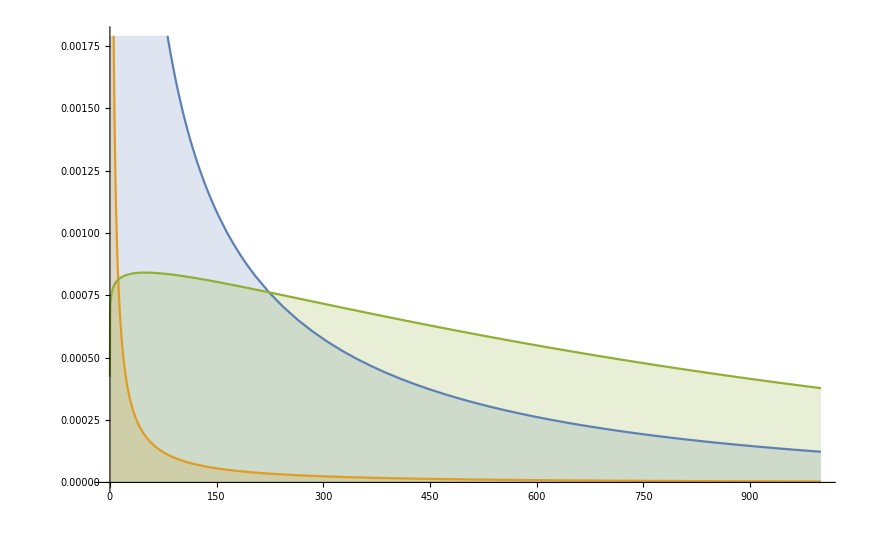

```mathematica
Plot[Evaluate@Table[PDF[GammaDistribution[α,1000],x],{α,{0.3,0.01, 1.05}}],{x,0,1000},Filling->Axis]
```

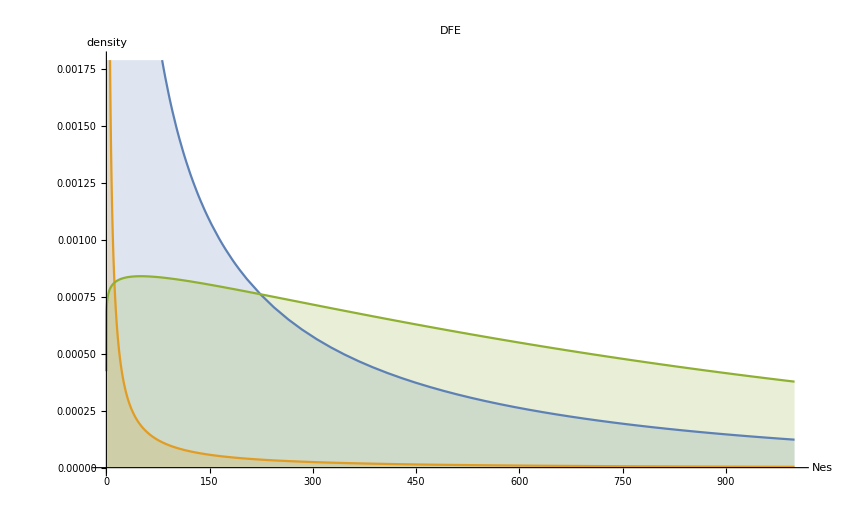

```mathematica
Show[%33,AxesLabel->{HoldForm[Nes],HoldForm[density]},PlotLabel->HoldForm[DFE],LabelStyle->{GrayLevel[0],Italic}]
```

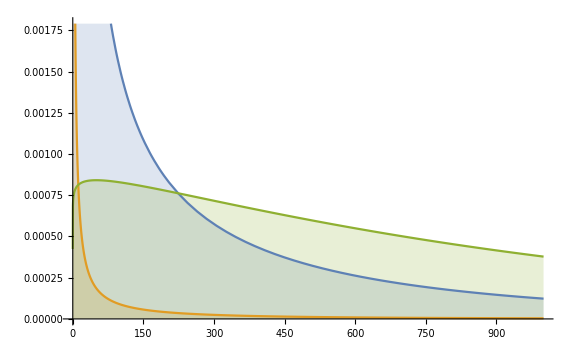

```mathematica
Show[%66,ImageSize->Large]
```

```mathematica
Export["/media/dsax/el extra/Dropbox/TESIS/10-01-16_MAT&MET/dfe.png",%63,"PNG"]
```

/media/dsax/el extra/Dropbox/TESIS/10-01-16_MAT&MET/dfe.png